## Start File for Escher Motiefs.

Save this file under a new name for your various "experiments"

Double Click on Brace (with little check mark at bottom) to the left to open

## Make Your Own Motief Make a SuperTile Tile with the SuperTile.

### myMotief --- Make Your Own

```mathematica
myMotief = {
			(* Fill in Your Own Design *)
			Text[ "Fill in Your Own Design", {.5, 0.5} ]
		};



(*............ You Don't need to change anything below this line ..........*)

	(* Setting the "Graph Paper"
          1 x 1 square
  *)
settingGraph = {
				 PlotRange-> { {0,1}, {0,1}},
				AspectRatio-> 1,
				Axes-> True
			};



	(* Grid lines *)
gridLines = {   Dashed,
			Table[ Line[ {  {0,i},{1,i}  } ],
				{i,0,1, 0.1}
				],
			Table[ Line[ {  {i,0},{i,1}  } ],
				{i,0,1, 0.1}
				]
		};

Graphics[ {
			gridLines ,
			myMotief
		}, 
			settingGraph
		]
```

### Creates and Shows the 8 Rotations and Reflections of Your Motief.

```mathematica
(* changing name to match closer to name "A" in 
		Schattschneider article *)
AMyMotief =myMotief;


		(* Rotate Pi/2 = 90 Degrees
				Through the middle - which is the point {1/2, 1/2}
	*)
BMyMotief = GeometricTransformation[  AMyMotief,
				RotationTransform[ Pi/2, {1/2, 1/2}]
				];
CMyMotief = GeometricTransformation[  AMyMotief,
				RotationTransform[ Pi, {1/2, 1/2}]
				];
DMyMotief = GeometricTransformation[  AMyMotief,
				RotationTransform[ 3Pi/2, {1/2, 1/2}]
				];

		(* Reflect through a Horizontal line through the point {1/2,1/2} *)
aMyMotief = GeometricTransformation[  AMyMotief,
				ReflectionTransform[ {0,1}, {1/2, 1/2}]
				];
	(* Reflect through the major diagonal through the point {1/2,1/2} *)
bMyMotief = GeometricTransformation[  AMyMotief,
				ReflectionTransform[ {1,1}, {1/2, 1/2}]
				];
	(* Reflect through a Vertical line through the point {1/2,1/2} *)
cMyMotief = GeometricTransformation[  AMyMotief,
				ReflectionTransform[ {1,0}, {1/2, 1/2}]
				];

	(* Reflect through the minor diagonal through the point {1/2,1/2} *)
dMyMotief = GeometricTransformation[  AMyMotief,
				ReflectionTransform[ {1,-1}, {1/2, 1/2}]
				];

	(* removed gridlines and setting *)	
GraphicsGrid[ {
			{ Graphics[AMyMotief],  Graphics[BMyMotief],  Graphics[CMyMotief],  Graphics[DMyMotief]},
			{  Graphics[aMyMotief],  Graphics[bMyMotief],  Graphics[cMyMotief], Graphics[dMyMotief]}
		}
		]
```

### SuperTile - Put together 4 Aspects of MyMotief

```mathematica
(* Decide which aspects you want and put them in below *)
superTile = {
			AMyMotief,
			Translate[aMyMotief, {1,0} ],
			Translate[AMyMotief, {0, -1}],
			Translate[aMyMotief, {1,-1}]
		};

Graphics[ superTile]
```

### Tile with the SuperTile

```mathematica
Graphics[ Table[
				Translate[ superTile, {2x,2y}],
				{x,0,2}, {y,0,2} 
			]
		]
```

## Using Trignometric Functions to make an n - gon - Cyclic Group

### A 7 - gon; points; line; 1/7 th triangle

```mathematica
numberOfSides = 7;

pointsAroundACircle = Table[   {Cos[ i * 2 Pi/numberOfSides], Sin[ i * 2Pi/numberOfSides]},
							{i, 0, numberOfSides}]

gridForCircle = {   Dashed,
			Table[ Line[ {  {-1,i},{1,i}  } ],
				{i,-1,1, 0.1}
				],
			Table[ Line[ {  {i,-1},{i,1}  } ],
				{i,-1,1, 0.1}
				]
		};

Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}]
			} 
	}, Axes-> True]
```

### a motief in the triangle Group C7 -- Rotations only

Examine the coordinates in the "yellow Triangle" = Fundamental Domain
   in order to draw a figure in it.

```mathematica
eFF = {
		{.5,0}, {.5,.5}, {.7, .5}, {.7, .4},
				{.6,.4}, {.6, .3}, {.7, .3}, 
				{.7, .2}, {.6, .2}, {.6, 0},
		{.5, 0}
	};




Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}],

			{Opacity[.7],Black,Thick,Polygon[eFF]}
			} 
	}, Axes-> True]
```

### Rotate EFF

```mathematica
eFF = {
		{.5,0}, {.5,.5}, {.7, .5}, {.7, .4},
				{.6,.4}, {.6, .3}, {.7, .3}, 
				{.7, .2}, {.6, .2}, {.6, 0},
		{.5, 0}
	};


	(* Eff and 2 Rotations *)
eFFred = {Opacity[.7],Red,Thick,Polygon[eFF]};

rotatedEFF = GeometricTransformation[  eFFred,
				RotationTransform[  2Pi/numberOfSides , {0,0} ]
					];
rotated2EFF = GeometricTransformation[  eFFred,
				RotationTransform[  2* 2Pi/numberOfSides , {0,0} ]
					];

reflectedEFF = GeometricTransformation[  eFFred,
				ReflectionTransform[  RotateLeft[pointsAroundACircle[[3]]]   ]
					];
	(* a Table of all the rotations *)
allRotations = Table[
					GeometricTransformation[  eFFred,
						RotationTransform[  i *2Pi/numberOfSides , {0,0} ]
					],
						{i, 0, numberOfSides-1}
				];


	(* Showing all Rotations -
        Getting rid of extraneous gridlines etc
	*)
Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}],

			eFFred,
			rotatedEFF,
			rotated2EFF

			} 
	}, Axes-> True]

Graphics[{    allRotations
	}]
```

### 7 Reflections of EFF

```mathematica
eFF = {
		{.5,0}, {.5,.5}, {.7, .5}, {.7, .4},
				{.6,.4}, {.6, .3}, {.7, .3}, 
				{.7, .2}, {.6, .2}, {.6, 0},
		{.5, 0}
	};


	(* Eff and 2 Rotations *)
eFFred = {Opacity[.7],Red,Thick,Polygon[eFF]};

rotatedEFF = GeometricTransformation[  eFFred,
				RotationTransform[  2Pi/numberOfSides , {0,0} ]
					];
rotated2EFF = GeometricTransformation[  eFFred,
				RotationTransform[  2* 2Pi/numberOfSides , {0,0} ]
					];

reflectedEFF = GeometricTransformation[  eFFred,
				ReflectionTransform[  RotateLeft[pointsAroundACircle[[3]]]   ]
					];


Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}],

	

Table[
		GeometricTransformation[  eFFred,
				ReflectionTransform[  RotateLeft[{-1,1}*pointsAroundACircle[[k]]]   ]
					], 
{k,1,7}]


			} 
	}, Axes-> True]
```

### Make Your Own Motief

#### First choose number of sides

```mathematica
(* Choose the number of Sides you want *)
numberOfSides = 4;


	(*..................Don't Change................*)
pointsAroundACircle = Table[   {Cos[ i * 2 Pi/numberOfSides], Sin[ i * 2Pi/numberOfSides]},
							{i, 0, numberOfSides}];

gridForCircle = {   Dashed,
			Table[ Line[ {  {-1,i},{1,i}  } ],
				{i,-1,1, 0.1}
				],
			Table[ Line[ {  {i,-1},{i,1}  } ],
				{i,-1,1, 0.1}
				]
		};

Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}]
			} 
	}, Axes-> True]
```

#### Create Your Motief in the Yellow Triangle. a motief in the triangle

Examine the coordinates in the "yellow Triangle" = Fundamental Domain
   in order to draw a figure in it.

```mathematica
myMotief = {
		Text[ "Draw Something", {0.1, 0.1}, {-1,0}]
	};


	(*.................Don't Change...........*)
Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}],

			{Opacity[.7],Black,Thick,myMotief}
			} 
	}, Axes-> True]
```

#### Rotate Your Motief

```mathematica
(* a Table of all the rotations *)
allRotations = Table[
					GeometricTransformation[  myMotief,
						RotationTransform[  i *2Pi/numberOfSides , {0,0} ]
					],
						{i, 0, numberOfSides-1}
				];


	(* Showing all Rotations -
        Getting rid of extraneous gridlines etc
	*)

Graphics[{    allRotations
	}]
```

## Using Trignometric Functions to make an n - gon - Dihedral Group

The Dihedral Group has: n reflections and n rotations for a total of 2n symmetries

```mathematica
numberOfSides = 7;

pointsAroundACircle = Table[   {Cos[ i * 2 Pi/(2 *numberOfSides)], Sin[ i * 2Pi/(2 * numberOfSides)]},
							{i, 0, 2 * numberOfSides}]

gridForCircle = {   Dashed,
			Table[ Line[ {  {-1,i},{1,i}  } ],
				{i,-1,1, 0.1}
				],
			Table[ Line[ {  {i,-1},{i,1}  } ],
				{i,-1,1, 0.1}
				]
		};

Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}]
			} 
	}, Axes-> True]
```

### a motief in the triangle Group D7

Examine the coordinates in the "yellow Triangle" = Fundamental Domain
   in order to draw a figure in it.

```mathematica
eFF = {
		{.65,0}, {.65, .3}, {.8, .3}, {.8, .25}, {.7, .25},
				{.7, .2}, {.8, .2}, {.75, .15}, {.7, .15},
				{.7, .0},
				{.65,0}
	};




Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}],

			{Opacity[.7],Blue,Thick,Polygon[eFF]}



			} 
	}, Axes-> True]
```

### Reflect the motief once

```mathematica
eFF = {
		{.65,0}, {.65, .3}, {.8, .3}, {.8, .25}, {.7, .25},
				{.7, .2}, {.8, .2}, {.75, .15}, {.7, .15},
				{.7, .0},
				{.65,0}
	};

eFFReflected = {Red, Opacity[.5],
GeometricTransformation[  Polygon[eFF],
		ReflectionTransform[RotateLeft[pointsAroundACircle [[2]]*{-1,1}]]]
}


Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}],

			{Opacity[.7],Blue,Thick,Polygon[eFF]}
,
eFFReflected

			} 
	}, Axes-> True
]
```

### Rotate eFF and its Reflection

```mathematica
eFF = {
		{.65,0}, {.65, .3}, {.8, .3}, {.8, .25}, {.7, .25},
				{.7, .2}, {.8, .2}, {.75, .15}, {.7, .15},
				{.7, .0},
				{.65,0}
	};

eFFReflected = {Red, Opacity[.5],
GeometricTransformation[  Polygon[eFF],
		ReflectionTransform[RotateLeft[pointsAroundACircle [[2]]*{-1,1}]]]
};


twoImages = {Polygon[eFF], eFFReflected};


Graphics[{Table[
		GeometricTransformation[ twoImages,
			RotationTransform[ i 2 Pi/numberOfSides ]
				],
			{i,0,numberOfSides-1}]
			
	}
]
```

### Make yout own Motief

#### First choose a number (it will be doubled)

```mathematica
(*.....................Choose a number .............*)
numberOfSides = 4;


(*................ Don't Change............*)
pointsAroundACircle = Table[   {Cos[ i * 2 Pi/(2 *numberOfSides)], Sin[ i * 2Pi/(2 * numberOfSides)]},
							{i, 0, 2 * numberOfSides}];

gridForCircle = {   Dashed,
			Table[ Line[ {  {-1,i},{1,i}  } ],
				{i,-1,1, 0.1}
				],
			Table[ Line[ {  {i,-1},{i,1}  } ],
				{i,-1,1, 0.1}
				]
		};

Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}]
			} 
	}, Axes-> True]
```

#### Create Your Motief in the Yellow Triangle.

Examine the coordinates in the "yellow Triangle" = Fundamental Domain
   in order to draw a figure in it.

```mathematica
myMotief = {
		Text[ "Draw Something", {0.1, 0.1}, {-1,0}]
		};


	(*.................Don't Change...........*)
Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
							pointsAroundACircle[[1]], 
							pointsAroundACircle[[2]]
						}],

			{Opacity[.7],Black,Thick,myMotief}
			} 
	}, Axes-> True]
```

#### Reflect the motief once

```mathematica
(* Reflecting *)
myMotiefReflected = GeometricTransformation[ myMotief,
					ReflectionTransform[{1,-1}*RotateLeft[pointsAroundACircle [[2]]]     ]];
					
Graphics[{
			gridForCircle,

			PointSize[0.03],
			{Red, Point[ pointsAroundACircle]},
			{Blue, Line[ pointsAroundACircle]},
			{Opacity[0.4,Yellow], Polygon[{ {0,0}, 
										pointsAroundACircle[[1]], 
										pointsAroundACircle[[2]]
										}]
			},
			myMotief,
			myMotiefReflected
			
		},
		 Axes-> True
		]
```

#### Rotate Your Motief and its Reflection

```mathematica
(* a Table of all the rotations *)
allRotations = Table[
					GeometricTransformation[  {myMotief, myMotiefReflected},
						RotationTransform[  i *2Pi/numberOfSides , {0,0} ]
					],
						{i, 0, numberOfSides-1}
				];


	(* Showing all Rotations -
        Getting rid of extraneous gridlines etc
	*)

Graphics[{    allRotations
	}]
```

## Illustrations (to be discussed in class)

## Escher's Motief - its' 8 Aspects - making a super tile

### 10 by 10 Grid -- This will create a 10x10 Graph paper.

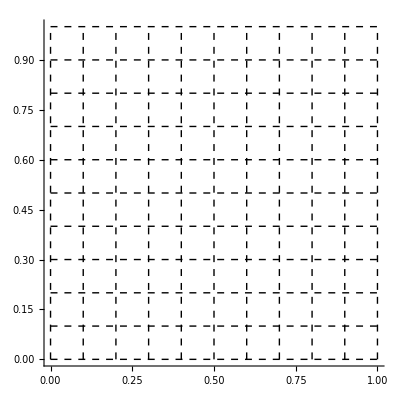

```mathematica
(* Setting the "Graph Paper"
          1 x 1 square
  *)
settingGraph = {
				 PlotRange-> { {0,1}, {0,1}},
				AspectRatio-> 1,
				Axes-> True
			};



	(* Grid lines *)
gridLines = {   Dashed,
			Table[ Line[ {  {0,i},{1,i}  } ],
				{i,0,1, 0.1}
				],
			Table[ Line[ {  {i,0},{i,1}  } ],
				{i,0,1, 0.1}
				]
		};

Graphics[ {
			gridLines 
		}, 
			settingGraph
		]
```

### 5 by 5 Grid -- This will create a 5x5 graph paper.

```mathematica
settingGraph = {
				 PlotRange-> { {0,1}, {0,1}},
				AspectRatio-> 1,
Axes-> True
			
			};




gridLines = {   Dashed,
			Table[ Line[ {  {0,i},{1,i}  } ],
				{i,0,1, 0.2}
				],
			Table[ Line[ {  {i,0},{i,1}  } ],
				{i,0,1, 0.2}
				]
		};

Graphics[ {
			gridLines 
		}, 
			settingGraph
		]
```

### Basic Lines -- This illustrates the basic lines on Escher's motief.

```mathematica
basicLines = { Thickness[0.02], Black,

			Line[{    {0, .2}, {.2,0}  }],
			Line[{    {.8, 0}, {1,.2}  }],

			Line[{    {0,.4}, {1,.8}  }],
			Line[{    {.6, 0}, {.2,1}  }],

			Line[{    {.4, 0}, {0,.8}  }],
			Line[{    {0, .6}, {.8,1}  }],

			Line[{    {.4, 1}, {1,.4}  }],
			Line[{    {.6, 1}, {1,.6}  }]
			};



		(* This draws the basicLines on the graph paper *)
Graphics[ {
			gridLines ,
			basicLines


		}, 
			settingGraph
		]

		(* This draws 4 copies of the basicLines in a 2x2 Tile *)
Graphics[ { 
			basicLines,                                                 Translate[basicLines, {1,0}  ]  ,
			Translate[basicLines, {0,-1}],    Translate[basicLines, {1,-1}] 


	    }]
```

### Red 1937 Motief - top of page 15

```mathematica
red1937 = { Red,

			Polygon[{    {0,0}, {0, .2}, {.2,0} , {0,0} }],
			Polygon[{    {1,0}, {.8, 0}, {1,.2}, {1,0}  }],

	

			Polygon[{    {.4, 0}, {0,.8} , {0,1}, {.2, 1}  , {.6, 0}, {.4,0}  }],
			Polygon[{    {0, .6}, {.8,1} , {1,1} , {1,.8} , {0,.4}, {0, .6} }],

			Polygon[{    {.4, 1}, {1,.4} ,  {1,.6}  ,   {.6, 1}, {.4, 1}   }]
			};




Graphics[ {
			gridLines ,
			red1937


		}, 
			settingGraph
		]
```

### Red1937 Motief - Reflections and Rotations -- see page 15 of article --

```mathematica
(* changing name to match closer to name "A" in 
		Schattschneider article *)
Ared1937 = red1937 ;


		(* Rotate Pi/2 = 90 Degrees
				Through the middle - which is the point {1/2, 1/2}
	*)
Bred1937 = GeometricTransformation[  Ared1937,
				RotationTransform[ Pi/2, {1/2, 1/2}]
				];
Cred1937 = GeometricTransformation[  Ared1937,
				RotationTransform[ Pi, {1/2, 1/2}]
				];
Dred1937 = GeometricTransformation[  Ared1937,
				RotationTransform[ 3Pi/2, {1/2, 1/2}]
				];

		(* Reflect through a Horizontal line through the point {1/2,1/2} *)
ared1937 = GeometricTransformation[  Ared1937,
				ReflectionTransform[ {0,1}, {1/2, 1/2}]
				];
	(* Reflect through the major diagonal through the point {1/2,1/2} *)
bred1937 = GeometricTransformation[  Ared1937,
				ReflectionTransform[ {1,1}, {1/2, 1/2}]
				];
	(* Reflect through a Vertical line through the point {1/2,1/2} *)
cred1937 = GeometricTransformation[  Ared1937,
				ReflectionTransform[ {1,0}, {1/2, 1/2}]
				];

	(* Reflect through the minor diagonal through the point {1/2,1/2} *)
dred1937 = GeometricTransformation[  Ared1937,
				ReflectionTransform[ {1,-1}, {1/2, 1/2}]
				];

	(* removed gridlines and setting *)	
GraphicsGrid[ {
			{ Graphics[Ared1937],  Graphics[Bred1937],  Graphics[Cred1937],  Graphics[Dred1937]},
			{  Graphics[ared1937],  Graphics[bred1937],  Graphics[cred1937], Graphics[dred1937]}
		}
		]
```

-Graphics-

### SuperTile and Tiling

#### another superTile AAaa

```mathematica
superTile = {
			Ared1937,
			Translate[ared1937, {1,0} ],
			Translate[ared1937, {0, -1}],
			Translate[Ared1937, {1,-1}]
		};

Graphics[ superTile]
```

#### Another iling with superTile

```mathematica
Graphics[ Table[
				Translate[ superTile, {2x,2y}],
				{x,0,2}, {y,0,2} 
			]
		]
```

### Colored 1937 Motief

```mathematica
red1937 = { Pink,

			Polygon[{    {0,0}, {0, .2}, {.2,0} , {0,0} }],
			Polygon[{    {1,0}, {.8, 0}, {1,.2}, {1,0}  }],

	

			Yellow,Polygon[{    {.4, 0}, {0,.8} , {0,1}, {.2, 1}  , {.6, 0}, {.4,0}  }],
			Cyan,Polygon[{    {0, .6}, {.8,1} , {1,1} , {1,.8} , {0,.4}, {0, .6} }],

			Green, Polygon[{    {.4, 1}, {1,.4} ,  {1,.6}  ,   {.6, 1}, {.4, 1}   }]
			};




Graphics[ {
			gridLines ,
			red1937


		}, 
			settingGraph
		]
```

## Two Blue Lines- and Randomizing

### 2 Blue Lines -- 10 by 10 Grid

```mathematica
goingUp = {
				Line[ {  {0.5, 0}, {1, 0.5} } ],
				Line[ {  {0,0.5}, {0.5,1}  } ]
			};

goingDown = {
				Line[ {  {0.5, 0}, {0, 0.5} } ],
				Line[ {  {1,0.5}, {0.5,1}  } ]
			};






	(* Setting the "Graph Paper"
          1 x 1 square
  *)
settingGraph = {
				 PlotRange-> { {0,1}, {0,1}},
				AspectRatio-> 1,
				Axes-> True
			};



	(* Grid lines *)
gridLines = {   Dashed,
			Table[ Line[ {  {0,i},{1,i}  } ],
				{i,0,1, 0.1}
				],
			Table[ Line[ {  {i,0},{i,1}  } ],
				{i,0,1, 0.1}
				]
		};

{
Graphics[ {
			gridLines ,
			goingUp
		}, 
			settingGraph
		],
Graphics[ {
			gridLines ,
			goingDown
		}, 
			settingGraph
		]
}
```

#### A table 200 x20

```mathematica
Graphics[{ Blue, Thick,
			Table[   Translate[  RandomChoice[ {goingUp, goingDown}], {x,y}],
					{x,0, 20}, {y, 0, 20}
				]
	}]
```

## A 3D Motief

```mathematica
motief3D = {
			Tube[{  {1/2,1/2,0}, {1, 1/2, 1/2} },  .05],
			Tube[{  {1/2,0,1/2}, {1/2, 1/2, 1} },  .05],
			Tube[{  {0, 1/2,1/2}, {1/2, 1, 1/2} },  .05]
		};


Graphics3D[ motief3D , PlotRange-> { {0,1}, {0,1}, {0,1}}]
```